```mathematica
Clear[Lx,Ly,A,
sx2d,SX2D,sx2dp,SX2DP,
sy2d,SY2D,sy2dp,SY2DP,
cx2d,CX2D,cx2dp,CX2DP,
cy2d,CY2D,cy2dp,CY2DP,
cons,Cons]
```

```mathematica
Lx=16;
Ly=16;
A=Lx*Ly;
```

```mathematica
B=1/Ly;
```

```mathematica
(*--- We choose gauge A = (-By,0,0) ---*)
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
sx2d[i_Integer,j_Integer]=0;

Do[Do[{sx2d[j+k Lx,j+1+k Lx]=-I/2 Exp[I B k],sx2d[j+1+k Lx,j+k Lx]=I/2 Exp[-I B k]},{j,1,Lx-1}],{k,0,Ly-1}]

SX2D=Table[sx2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
sx2dp[i_Integer,j_Integer]=0;

Do[{sx2dp[(k+1)Lx,1+k Lx]=-I/2 Exp[I B k],sx2dp[1+k Lx,(k+1)Lx]=I/2 Exp[-I B k]},{k,0,Ly-1}]

SX2DP=Table[sx2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
sy2d[i_Integer,j_Integer]=0;

Do[Do[{sy2d[k Lx+j,(k+1)Lx+j]=-I/2,sy2d[(k+1)Lx+j,k Lx+j]=I/2},{j,1,Lx}],{k,0,Ly-2}]

SY2D=Table[sy2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
sy2dp[i_Integer,j_Integer]=0;

Do[{sy2dp[(Ly-1)Lx+j,j]=-I/2,sy2dp[j,(Ly-1)Lx+j]=I/2},{j,1,Lx}]

SY2DP=Table[sy2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
cx2d[i_Integer,j_Integer]=0;

Do[Do[{cx2d[j+k Lx,j+1+k Lx]=1/2 Exp[I B k],cx2d[j+1+k Lx,j+k Lx]=1/2 Exp[-I B k]},{j,1,Lx-1}],{k,0,Ly-1}]

CX2D=Table[cx2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
cx2dp[i_Integer,j_Integer]=0;

Do[{cx2dp[(1+k)Lx,1+k Lx]=1/2 Exp[I B k],cx2dp[1+k Lx,(1+k)Lx]=1/2 Exp[-I B k]},{k,0,Ly-1}]

CX2DP=Table[cx2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
cy2d[i_Integer,j_Integer]=0;

Do[Do[{cy2d[k Lx+j,(k+1)Lx+j]=1/2,cy2d[(k+1)Lx+j,k Lx+j]=1/2},{j,1,Lx}],{k,0,Ly-2}]

CY2D=Table[cy2d[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*--------------------------------------------------*)
```

```mathematica
cy2dp[i_Integer,j_Integer]=0;

Do[{cy2dp[(Ly-1)Lx+j,j]=1/2,cy2dp[j,(Ly-1)Lx+j]=1/2},{j,1,Lx}]

CY2DP=Table[cy2dp[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*--------------- Lattice model for a constant matrix ---------------*)
```

```mathematica
cons[i_Integer, j_Integer]:=0

Do[{cons[i,i]=1},{i,1,A}]

Cons=Table[cons[i,j],{i,1,A},{j,1,A}];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*-----------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[σ0,σ1,σ2,σ3,HamiltonianWSM1, HamiltonianWSM2]
```

```mathematica
σ0=PauliMatrix[0];
σ1=PauliMatrix[1];
σ2=PauliMatrix[2];
σ3=PauliMatrix[3];
```

```mathematica
(* HamiltonianQAHI[t_,t0_,m_,α_]:=t*(KroneckerProduct[SX2D+α*SX2DP,σ1]+KroneckerProduct[SY2D+α*SY2DP, σ2])+KroneckerProduct[-m*Cons+t0*(CX2D+CY2D+α*CX2DP+α*CY2DP),σ3] *)
```

```mathematica
(* HamiltonianQAHI[t_,t0_,m_,kz_]:=t*(KroneckerProduct[SX2D,σ1]+KroneckerProduct[SY2D, σ2])+KroneckerProduct[-m*Cons+t0*(CX2D+CY2D),σ3] +Cos[kz]*KroneckerProduct[Cons,σ3] *)
```

```mathematica
HamiltonianWSM1[t_,t0_,m_,tz_,kz_,αx_, αy_]:=t*(KroneckerProduct[SX2D+αx*SX2DP,σ1]+KroneckerProduct[SY2D+αy*SY2DP, σ2])+KroneckerProduct[2*Cons-t0*(CX2D+CY2D+αx*CX2DP+αy*CY2DP),σ3]+KroneckerProduct[(tz *Cos[kz]-m)*Cons,σ3]
```

```mathematica
HamiltonianWSM2[t_,m_,kz_,αx_, αy_,tz_]:=2t*(KroneckerProduct[SX2D+αx*SX2DP,σ1]+KroneckerProduct[SY2D+αy*SY2DP, σ2])+2m * KroneckerProduct[2*Cons-(CX2D+CY2D+αx*CX2DP+αy*CY2DP),σ3]+KroneckerProduct[(2 t *Cos[kz])*Cons,σ3]-2 tz * KroneckerProduct[SX2D+αx*SX2DP,σ0]
```

```mathematica
(*--------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[val,vec,ValVecAHI,ValAHI,ValAHIRange,β]
```

```mathematica
β=-1.75;
```

```mathematica
{val,vec}=Eigensystem[HamiltonianWSM1[1.,1.,0,1,(β π)/2,0,0]];
```

```mathematica
ValVecAHI=SortBy[Transpose[{val,vec}],First];
```

```mathematica
ValAHI=Table[{j,Re[ValVecAHI[[j,1]]]},{j,1,2A}];
```

```mathematica
ValAHIRange=Table[ValAHI[[j,2]],{j,1,2 A}];
```

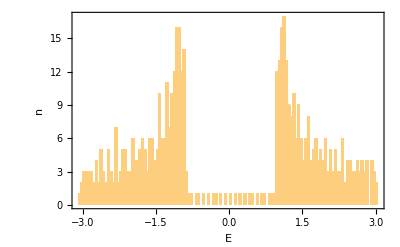

```mathematica
Show[Histogram[val,100],PlotRange-> All, Frame-> True, FrameLabel-> {"E","n"},BaseStyle-> 16,FrameStyle-> {{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}}]
```

```mathematica
(*zeroMagfield*)
```

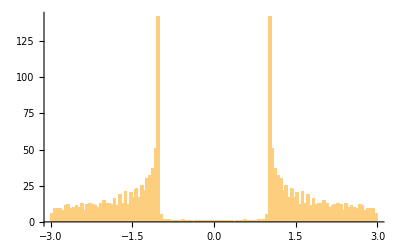

-Graphics-

```mathematica
(** B = 1 **)
```

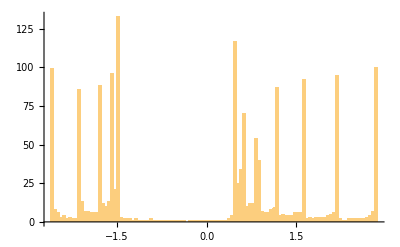

-Graphics-

```mathematica
(*--------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[val2,vec2,ValVecAHI2,ValAHI2,ValAHIRange2,β];
β=2;
```

```mathematica
{val2,vec2}=Eigensystem[HamiltonianWSM2[1.,3.,(β π)/2,0,0,0]];
```

```mathematica
ValVecAHI2=SortBy[Transpose[{val2,vec2}],First];
```

```mathematica
ValAHI2=Table[{j,Re[ValVecAHI2[[j,1]]]},{j,1,2A}];
```

```mathematica
ValAHIRange2=Table[ValAHI2[[j,2]],{j,1,2 A}];
```

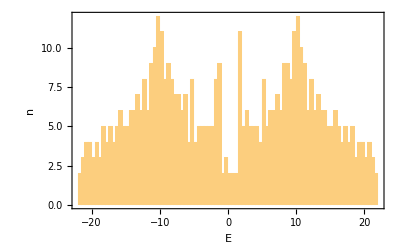

```mathematica
Show[Histogram[val2,100],PlotRange->All, Frame-> True, FrameLabel-> {"E","n"},BaseStyle-> 16,FrameStyle-> {{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}}]
```

```mathematica
Clear[kzVector]
```

```mathematica
kzVector = N@Subdivide[-π,π,50]
```

{-3.14159,-3.01593,-2.89027,-2.7646,-2.63894,-2.51327,-2.38761,-2.26195,-2.13628,-2.01062,-1.88496,-1.75929,-1.63363,-1.50796,-1.3823,-1.25664,-1.13097,-1.00531,-0.879646,-0.753982,-0.628319,-0.502655,-0.376991,-0.251327,-0.125664,0.,0.125664,0.251327,0.376991,0.502655,0.628319,0.753982,0.879646,1.00531,1.13097,1.25664,1.3823,1.50796,1.63363,1.75929,1.88496,2.01062,2.13628,2.26195,2.38761,2.51327,2.63894,2.7646,2.89027,3.01593,3.14159}

```mathematica
NumPoints=Dimensions[kzVector][[1]]
```

51

```mathematica
(** 
Clear[b];
b={};
Do[{Clear[a],
a=Eigenvalues[HamiltonianWSM1[1.,1.,0,1,kzVector[[i]],1,1]],
Do[b=Append[b,{kzVector[[i]],a[[j]]}],{j,1,2*A}]},{i,1,NumPoints}]  **)
```

```mathematica
(** listplotOfenergyWithKz=Show[ListPlot[b,PlotRange-> { {-3.14,3.14} ,{-1,1}}],AxesLabel-> {"kz","Energy"},Frame-> True] **)
```

```mathematica
(** Show[ListPlot[b,PlotRange->{{-3.14,3.14},{-1,1}}],AxesLabel->{"kz","Energy"},Frame->True] **)
```

```mathematica
(*Older plots - with -2t_0 SX periodic in x **)
```

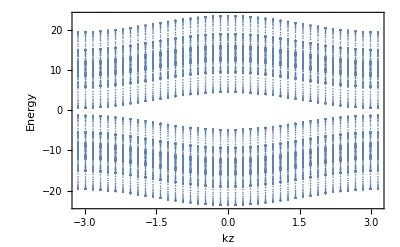

-Graphics-

-Graphics-

```mathematica
(** tz=0 **)
```

```mathematica
(** Clear[bb];
bb={};
Do[{Clear[a],
a=Eigenvalues[HamiltonianWSM2[1.,3.,kzVector[[i]],1,1,0]],
Do[bb=Append[bb,{kzVector[[i]],a[[j]]}],{j,1,2*A}]},{i,1,NumPoints}] **)
```

```mathematica
(** Show[ListPlot[bb,PlotRange-> { {-2.5,-1} ,{-0.5,0.5}},PlotStyle->PointSize[0.05]],AxesLabel-> {"kz","Energy"},Frame-> True] **)
```

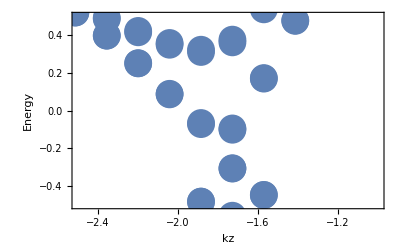

-Graphics-

```mathematica
(** Show[ListPlot[bb,PlotRange-> { {-3.14,3.14} ,{-2,2}},PlotStyle->PointSize[0.02]],AxesLabel-> {"kz","Energy"},Frame-> True] **)
```

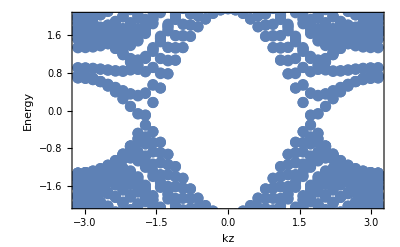

-Graphics-

```mathematica
(*Older plots - with -2t_0 SX periodic in y **)
```

-Graphics-

-Graphics-

```mathematica
(** tz=0.5 **)
```

```mathematica
(** Clear[bbb];
bbb={};
Do[{Clear[a],
a=Eigenvalues[HamiltonianWSM2[1.,3.,kzVector[[i]],1,1,0.5]],
Do[bbb=Append[bbb,{kzVector[[i]],a[[j]]}],{j,1,2*A}]},{i,1,NumPoints}] **)
```

```mathematica
(** Show[ListPlot[bbb,PlotRange-> { {-2.5,-1} ,{-0.5,0.5}},PlotStyle->PointSize[0.05]],AxesLabel-> {"kz","Energy"},Frame-> True] **)
```

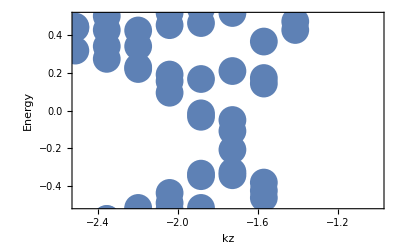

-Graphics-

```mathematica
(** Show[ListPlot[bbb,PlotRange-> { {-3.14,3.14} ,{-2,2}},PlotStyle->PointSize[0.02]],AxesLabel-> {"kz","Energy"},Frame-> True] **)
```

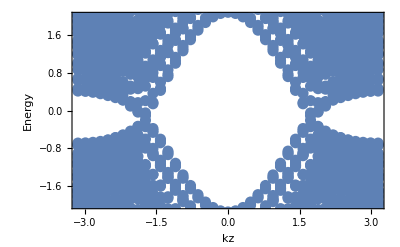

-Graphics-

```mathematica
(** tz=1 **)
```

```mathematica
(** Clear[bbbb];
bbbb={};
Do[{Clear[a],
a=Eigenvalues[HamiltonianWSM2[1.,3.,kzVector[[i]],1,1,1]],
Do[bbbb=Append[bbbb,{kzVector[[i]],a[[j]]}],{j,1,2*A}]},{i,1,NumPoints}] **)
```

```mathematica
(** Show[ListPlot[bbbb,PlotRange-> { {-2.5,-1} ,{-0.5,0.5}},PlotStyle->PointSize[0.05]],AxesLabel-> {"kz","Energy"},Frame-> True] **)
```

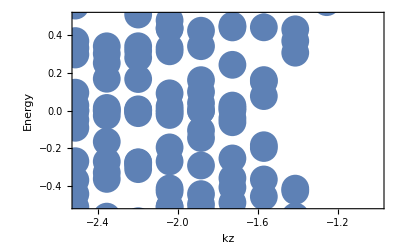

-Graphics-

```mathematica
(** Show[ListPlot[bbbb,PlotRange-> { {-3.14,3.14} ,{-2,2}},PlotStyle->PointSize[0.02]],AxesLabel-> {"kz","Energy"},Frame-> True] **)
```

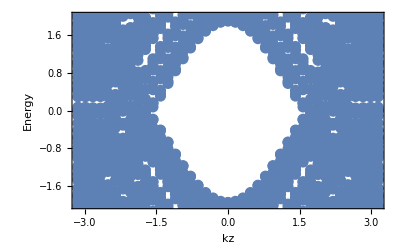

-Graphics-

```mathematica
(** tz=1.5 **)
```

```mathematica
(** Clear[bbbbb];
bbbbb={};
Do[{Clear[a],
a=Eigenvalues[HamiltonianWSM2[1.,3.,kzVector[[i]],1,1,1.5]],
Do[bbbbb=Append[bbbbb,{kzVector[[i]],a[[j]]}],{j,1,2*A}]},{i,1,NumPoints}] **)
```

```mathematica
(** Show[ListPlot[bbbbb,PlotRange-> { {-2.5,-1} ,{-0.5,0.5}},PlotStyle->PointSize[0.05]],AxesLabel-> {"kz","Energy"},Frame-> True] **)
```

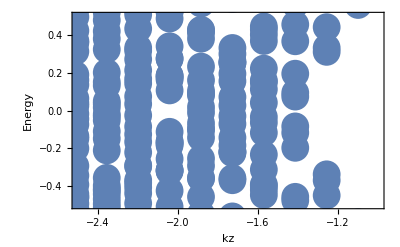

-Graphics-

```mathematica
(** Show[ListPlot[bbbbb,PlotRange-> { {-3.14,3.14} ,{-2,2}},PlotStyle->PointSize[0.02]],AxesLabel-> {"kz","Energy"},Frame-> True] **)
```

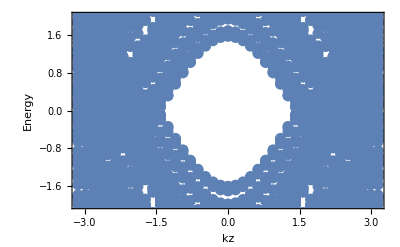

-Graphics-

```mathematica
(*--------------------quasicrystal--------------------------*)
```

```mathematica
Clear[Sitelocation,FlatSite,Sites, LineUp,LineDn]
```

```mathematica
Sitelocation=Table[{i,j},{i,1,Lx},{j,1,Ly}];
```

```mathematica
FlatSite=Flatten[Sitelocation];
```

```mathematica
NOrbitals=Dimensions[FlatSite][[1]]
```

512

```mathematica
Sites=Table[{FlatSite[[i]],FlatSite[[i+1]]},{i,1,NOrbitals,2}];
```

```mathematica
(**--Equations for the two red lines--**)
```

```mathematica
LineUp[x_]:=((1+√5)/2)^-1*(x-1)+8
LineDn[x_]:=((1+√5)/2)^-1*(x-2)+4
```

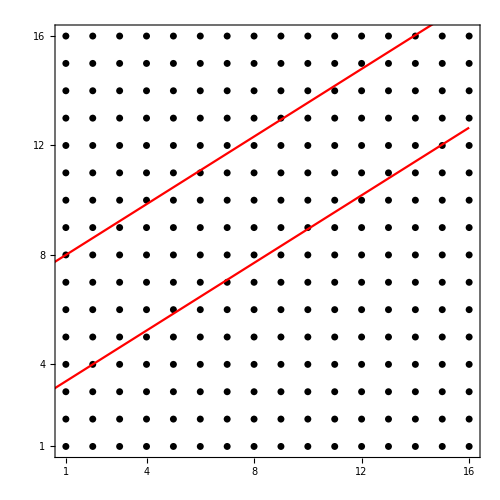

```mathematica
Show[ListPlot[Sites,PlotStyle-> {Black,PointSize[0.01]},Frame-> True,Axes-> False,PlotRange-> {{0.9,Lx+0.1},{0.9,Ly+0.1}}],
(*Plot[2/3*(x-1)+4,{x,0,Lx},PlotStyle-> Blue],Plot[2/3*(x-2)+3,{x,0,Lx},PlotStyle-> Blue],*)
Plot[LineUp[x],{x,0,Lx},PlotStyle-> Red],
Plot[LineDn[x],{x,0,Lx},PlotStyle-> Red],
FrameStyle-> {{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},BaseStyle-> 16,
FrameTicks-> {{{{1,"1"},{4,"4"},{8,"8"},{12,"12"},{16,"16"},{20,"20"}},None},{{{1,"1"},{4,"4"},{8,"8"},{12,"12"},{16,"16"},{20,"20"}},None}},
ImageSize-> 500,AspectRatio-> 1
]
```

```mathematica
(*-----------------------------------------------------------------------------*)
```

```mathematica
Clear[Fibonup,Fibondown,TotalFibon,XList, YList, XListKron, YListKron, Ux, Vy]
```

```mathematica
(**-----We want to count points inside the area of interest, store them in FibonupNew, and sort them into Fibonup-----**)
```

```mathematica
Clear[FibonupNew]
FibonupNew={};
```

```mathematica
(**---Points on the lines are not taken---**)
```

```mathematica
(**---That is why we calculate Floor[]+1 instead of Ceiling, and Ceiling[]-1 instead of Floor---**)
```

```mathematica
Do[Do[FibonupNew=Append[FibonupNew,x+(y-1)*Lx],{y,Max[1,Floor[LineDn[x]]+1],Min[Ly,Ceiling[LineUp[x]]-1]}],{x,1,Lx}]
```

```mathematica
FibonupNew;
```

```mathematica
Fibonlist=Sort[FibonupNew]
```

{49,65,66,67,81,82,83,84,85,97,98,99,100,101,102,114,115,116,117,118,119,120,131,132,133,134,135,136,137,138,149,150,151,152,153,154,155,166,167,168,169,170,171,172,173,184,185,186,187,188,189,190,202,203,204,205,206,207,208,219,220,221,222,223,224,237,238,239,240,254,255,256}

```mathematica
(** Fibonup2={}; **)
```

```mathematica
(** Do[Do[Fibonup2=Append[Fibonup2,x+(y-1)*Lx],{y,6,15}],{x,6,15}]**)
```

```mathematica
(** Fibonup2**)
```

```mathematica
(** Clear[Fibonup]**)
```

```mathematica
(** Fibonup = Fibonup2**)
```

```mathematica
YList = Ceiling[Fibonlist/Lx];
```

```mathematica
XList = Fibonlist - (YList - 1)Lx;
```

```mathematica
(**Check that the list is correct**)
```

```mathematica
XList + (YList-1)*Lx - Fibonlist
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
XListKron = Flatten[KroneckerProduct[XList,{1,1}],2];
```

```mathematica
YListKron = Flatten[KroneckerProduct[YList,{1,1}],2];
```

```mathematica
Ux =DiagonalMatrix[ Exp[2 π I XListKron /Lx]];
```

```mathematica
Vy = DiagonalMatrix[Exp[2 π I YListKron/Ly]];
```

```mathematica
(**--Compare with the previous (manually calculated) Fibonup for 20x20 sites--**)
```

```mathematica
(**--Fibonup={1,22,23,43,44,45,65,66,86,87,88,108,109,110,130,131,151,152,153,173,174,194,195,196,216,217,218,238,239,259,260};--**)
```

```mathematica
(**----Group the orbitals in the sites in Fibonlist ---**)
```

```mathematica
Fibonup = 2 * Fibonlist -1;
```

```mathematica
Fibondown = 2 * Fibonlist;
```

```mathematica
(**-- Fibondown=Table[Fibonlist[[j]]+A,{j,1,Dimensions[Fibonlist][[1]]}]; --**)
```

```mathematica
TotalFibon=Flatten[{Fibonup,Fibondown}];
```

```mathematica
TotalFibon = Sort[TotalFibon]
```

{97,98,129,130,131,132,133,134,161,162,163,164,165,166,167,168,169,170,193,194,195,196,197,198,199,200,201,202,203,204,227,228,229,230,231,232,233,234,235,236,237,238,239,240,261,262,263,264,265,266,267,268,269,270,271,272,273,274,275,276,297,298,299,300,301,302,303,304,305,306,307,308,309,310,331,332,333,334,335,336,337,338,339,340,341,342,343,344,345,346,367,368,369,370,371,372,373,374,375,376,377,378,379,380,403,404,405,406,407,408,409,410,411,412,413,414,415,416,437,438,439,440,441,442,443,444,445,446,447,448,473,474,475,476,477,478,479,480,507,508,509,510,511,512}

```mathematica
NOrbitalsQuasi=Dimensions[TotalFibon][[1]]
```

144

```mathematica
NOrbitalsQuasi/2
```

72

```mathematica
NOrbitalsOutside = NOrbitals-NOrbitalsQuasi
```

368

```mathematica
PercentageDataIn = N[NOrbitalsQuasi/(2*A)]
```

0.28125

```mathematica
Clear[F1,a]
```

```mathematica
F1=Table[i,{i,1,2*A}];
```

```mathematica
Dimensions[F1]
```

{512}

```mathematica
(**-- a=F1;
Do[
a=Drop[a,{TotalFibon[[NOrbitalsQuasi-i]]}],
{i,0,NOrbitalsQuasi-1,1}
] --**)
```

```mathematica
a= Complement[F1, TotalFibon];
```

```mathematica
(**-------------------------------**)
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[TabRenorEnergies]
```

```mathematica
TabRenorEnergies={}
```

{}

```mathematica
Do[{Clear[HTrial,Hfbfb,HFBFB,H2d2d,H2D2D,H2dfb,H2DFB,Hfb2d,HFB2D],
(**HTrial=HamiltonianWSM2[1.,3.,kzVector[[p]],0,0,0],**)
HTrial = HamiltonianWSM1[1,1,0,1,kzVector[[p]],1,0],
(*---------------------------------------------------------*)
Hfbfb[i_Integer,j_Integer]=0,
Do[
Do[
Hfbfb[i,j]=HTrial[[TotalFibon[[i]],TotalFibon[[j]]]],
{i,1,NOrbitalsQuasi}
],
{j,1,NOrbitalsQuasi}
],
HFBFB=Table[Hfbfb[i,j],{i,1,NOrbitalsQuasi},{j,1,NOrbitalsQuasi}],
(*---------------------------------------------------------*)
H2d2d[i_Integer,j_Integer]=0,
Do[
Do[
H2d2d[i,j]=HTrial[[a[[i]],a[[j]]]],
{i,1,NOrbitalsOutside}
],
{j,1,NOrbitalsOutside}
],
H2D2D=Table[H2d2d[i,j],{i,1,NOrbitalsOutside},{j,1,NOrbitalsOutside}],
(*------------------------------------------------------*)
H2dfb[i_Integer,j_Integer]=0,

Do[
Do[
H2dfb[i,j]=HTrial[[a[[i]],TotalFibon[[j]]]],
{i,1,NOrbitalsOutside}
],
{j,1,NOrbitalsQuasi}
],
H2DFB=Table[H2dfb[i,j],{i,1,NOrbitalsOutside},{j,1,NOrbitalsQuasi}],
(*-------------------------------------------------*)
Hfb2d[i_Integer,j_Integer]=0,

Do[
Do[
Hfb2d[i,j]=HTrial[[TotalFibon[[i]],a[[j]]]],
{i,1,NOrbitalsQuasi}
],
{j,1,NOrbitalsOutside}
],
HFB2D=Table[Hfb2d[i,j],{i,1,NOrbitalsQuasi},{j,1,NOrbitalsOutside}],

(*---------------------------------------------------------------------------------------------------------------------------------*)
Clear[HFibonRenor,ValueFibon,VecFibon,ValVecFibon,ValFibon],
HFibonRenor=HFBFB-(HFB2D.Inverse[H2D2D].H2DFB),
(**------Check that HFibonRenor is Hermitian------**)
OnlyEigenvalue=Eigenvalues[HFibonRenor],
percentageOfOrbitalsInside = N[NOrbitalsQuasi/(2*A)],
NSitesInside = NOrbitalsQuasi/2,
Do[TabRenorEnergies = Append[TabRenorEnergies,{kzVector[[p]],OnlyEigenvalue[[i]]}],{i,1,NOrbitalsQuasi}]
},{p,2,NumPoints-1}]
```

```mathematica
TabRenorEnergies=Sort[Re[TabRenorEnergies]];
```

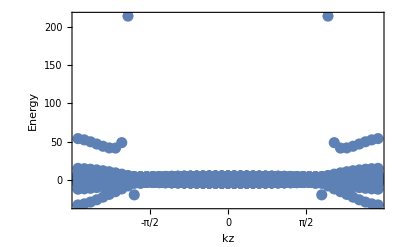

```mathematica
Show[ListPlot[Re[TabRenorEnergies],PlotRange-> All,PlotStyle->PointSize[0.02]],FrameTicks-> {{-π,-π/2,0,π/2,π},Automatic,{},{}},BaseStyle-> 18,AxesLabel-> {"kz","Energy"},Frame-> True]
```

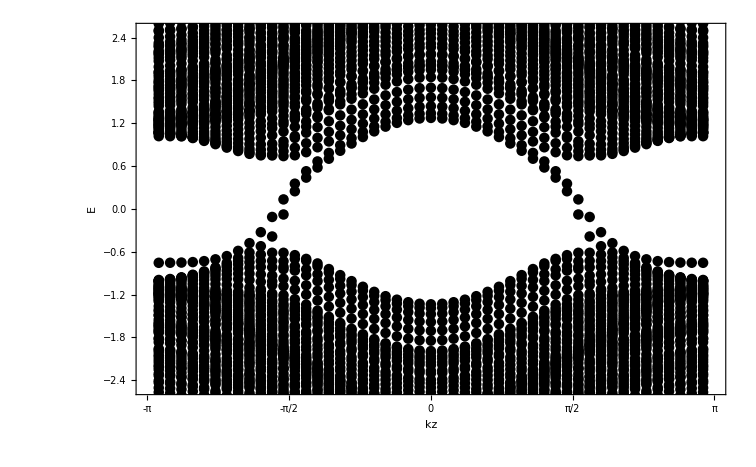

```mathematica
A=Show[ListPlot[Re[TabRenorEnergies],PlotRange-> { {-π,π} ,{-2.5,2.5}},PlotStyle->{PointSize[0.01],Black}],FrameTicks-> {{-π,-π/2,0,π/2,π},Automatic,{},{}},BaseStyle-> 18,FrameLabel-> {"kz","E"},Frame-> True]
```

```mathematica
(** 15x15 parent lattice **)
```

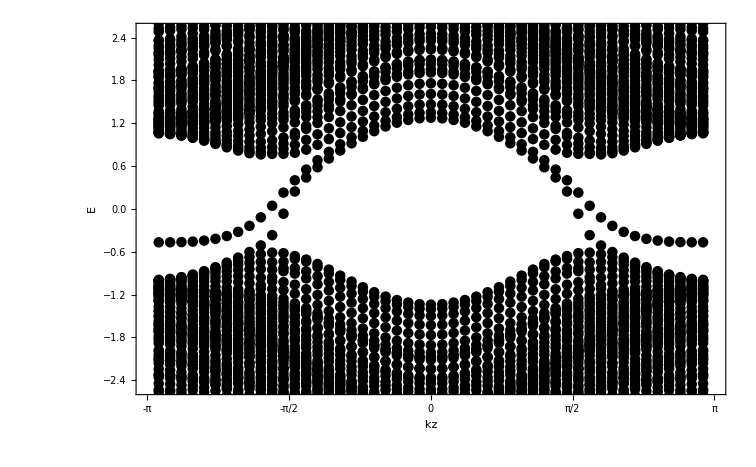

-Graphics-

```mathematica
(** Export["FibonEnergies32x32-linUp+14linDn-4Magnetic1byLy-xPeriod-yOpenPRLModel.dat",TabRenorEnergies] **)
```

```mathematica
Dimensions[TabRenorEnergies]
```

{7056,2}

```mathematica
Dimensions[kzVector][[1]]*NOrbitalsQuasi
```

7344

```mathematica
TabRenorEnergies[[NOrbitalsQuasi/2 +1]]
```

{-3.01593,-0.753784}

```mathematica
{LandauLevelEnergies1 = {},Do[LandauLevelEnergies1 = Append[LandauLevelEnergies1, TabRenorEnergies[[NOrbitalsQuasi/2+1+k*NOrbitalsQuasi]]],{k,0,Dimensions[kzVector][[1]]-3}]};
```

```mathematica
{LandauLevelEnergies2 = {},Do[LandauLevelEnergies2 = Append[LandauLevelEnergies2, TabRenorEnergies[[NOrbitalsQuasi/2+3+k*NOrbitalsQuasi]]],{k,0,Dimensions[kzVector][[1]]-3}]};
```

```mathematica
LandauLevelEnergies
```

LandauLevelEnergies

```mathematica
LandauLevelEnergies
```

LandauLevelEnergies

```mathematica
(** Export["LandauLevelFibonEnergies32x32-linUp+14linDn-4Magnetic1byLy-xPeriod-yOpenPRLModel.dat",LandauLevelEnergies]; **)
```

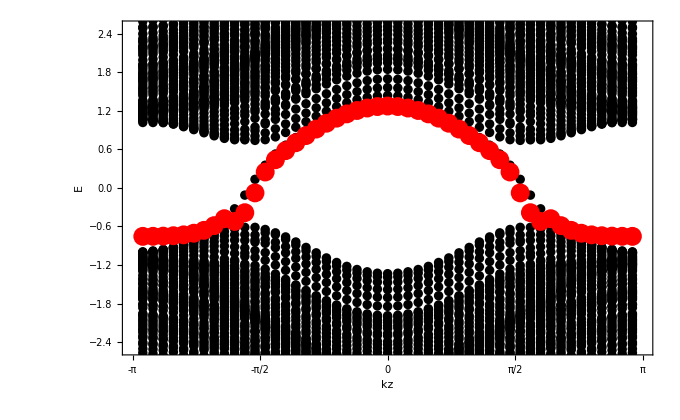

```mathematica
Show[A,ListPlot[Re[LandauLevelEnergies1],PlotStyle->{Red,PointSize[0.02]},PlotRange->{{-π/2,π/2},All}],FrameStyle-> {Black,Black,Black,Black}]
```

```mathematica
A1=ListPlot[Re[LandauLevelEnergies2],PlotStyle->{Red,PointSize[0.02]},PlotRange->{{-π,-π/2},All}];
```

```mathematica
A2=ListPlot[Re[LandauLevelEnergies2],PlotStyle->{Red,PointSize[0.02]},PlotRange->{{π/2,π},All}];
```

```mathematica
A3=ListPlot[Re[LandauLevelEnergies1],PlotStyle->{Red,PointSize[0.02]},PlotRange->{{-π/2,π/2},All}];
```

```mathematica
Show[A,A1,A2,A3];
```

```mathematica
(** LineUp[x_]:=((1+√5)/2)^-1*(x-1)+4
LineDn[x_]:=((1+√5)/2)^-1*(x-2)-2 for 28x28 **)
```

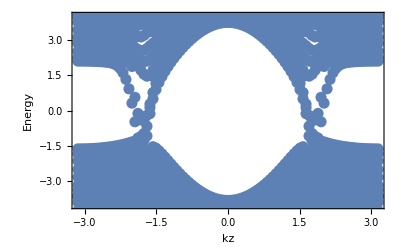

-Graphics-

```mathematica
(** TabRenorEnergiesPlus4Minus2 **)
```

```mathematica
TabRenorEnergiesPlus4Minus2
```

TabRenorEnergiesPlus4Minus2

```mathematica
(** LineUp[x_]:=((1+√5)/2)^-1*(x-1)+4
LineDn[x_]:=((1+√5)/2)^-1*(x-2)-2 for 20x20 **)
```

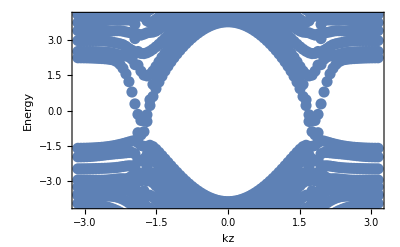

-Graphics-

```mathematica
(** TabRenorEnergiesPlus14Minus4 **)
```

```mathematica
(** LineUp[x_]:=((1+√5)/2)^-1*(x-1)+14
LineDn[x_]:=((1+√5)/2)^-1*(x-2)-4 for 20x20 **)
```

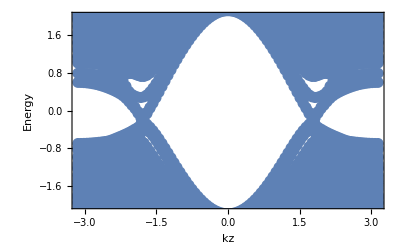

-Graphics-

```mathematica
(** LineUp[x_]:=((1+√5)/2)^-1*(x-1)+4
LineDn[x_]:=((1+√5)/2)^-1*(x-2)+2 **)
```

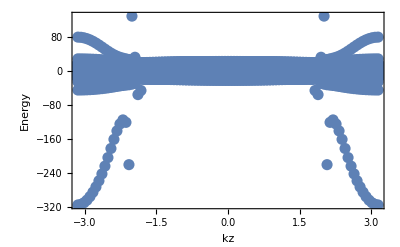

-Graphics-